<|
"Title"→"Plotting",
"Slug"→Automatic,
"Path"→"Using Mathematica/Useful Features",
"ID"→"1.3.1",
"Date"→Now,
"Modified"→Now,
"Authors"→{},
"Categories"→{"using-mathematica","useful-features"},
"Tags"→{"plotting"}
|>

### Plotting

Mathematica has a host of different plot functions, but usually one only needs three of them:

#### Plot

Plot takes a function as its first argument and a variable and range as its second one. Example:

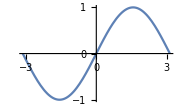

```mathematica
Plot[Sin[x],{x,-π,π},
ImageSize->Small]
```

The function can also be defined outside of the Plot function itself:

```mathematica
sinx=Sin[x];
Plot[sinx,{x,-π,π},
ImageSize->Small]
```

-Graphics-

User defined functions are also valid, but they must first be called on the variable one wants to use.

That’s why the following fails:

```mathematica
mySin[x_]:=Sin[x];
Plot[mySin,{x,-π,π},
ImageSize->Small]
```

-Graphics-

But the following will work:

```mathematica
mySin[x_]:=Sin[x];
Plot[mySin[x],{x,-π,π},
ImageSize->Small]
```

-Graphics-

Plot can also plot many functions simultaneously, if the first argument is a list of appropriate functions:

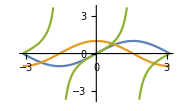

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]},{x,-π,π},
ImageSize->Small]
```

These functions can be distinguished from each other via legends and styling. For example:

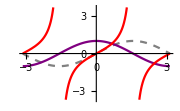

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]},{x,-π,π},
PlotLegends->"Expressions",
PlotStyle->{
Directive[Dashed,Gray],
Directive[Thick,Purple],
Directive[Thin,Red]
},
ImageSize->Small
]
```

#### ListPlot

ListPlot is a variant of Plot that just takes a list of values and plots them. For example, let’s plot the first 1000 primes. The function we’re using here, Table, is explained more in the next section.

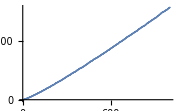

```mathematica
ListPlot[Table[Prime[n],{n,1000}],
ImageSize->Small]
```

Similarly to Plot, we can plot multiple data sets:

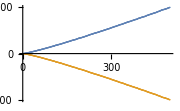

```mathematica
ListPlot[{
Table[Prime[n],{n,Range[2,1000,2]}],
Table[-Prime[n],{n,Range[1,999,2]}]},
ImageSize->Small]
```

And again we can apply styling rules:

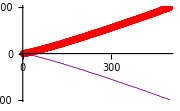

```mathematica
ListPlot[{
Table[Prime[n],{n,Range[2,1000,2]}],
Table[-Prime[n],{n,Range[1,999,2]}]},
PlotLegends->{"prime_n for n=2,4,6,...,1000",
"-prime_n for n=1,3,5,...,999"},
PlotStyle->{Directive[AbsolutePointSize[5],Red],Directive[AbsolutePointSize[.1],Purple]},
ImageSize->Small
]
```

We can also join the points to plot out a line

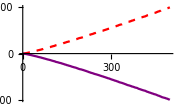

```mathematica
ListPlot[{
Table[Prime[n],{n,Range[2,1000,2]}],
Table[-Prime[n],{n,Range[1,999,2]}]},
PlotLegends->{"prime_n for n=2,4,6,...,1000",
"-prime_n for n=1,3,5,...,999"},
PlotStyle->{Directive[Dashed,Red],Directive[Thick,Purple]},
Joined->True,
ImageSize->Small
]
```

#### Plot3D

Plot3D works just like Plot, but takes two ranges

```mathematica
Plot3D[Sin[x+y],{x,-π,π},{y,0,2π},
ImageSize->Small]
```

-Graphics3D-

Multiple functions:

```mathematica
Plot3D[{Sin[x],Cos[y]},{x,-π,π},{y,0,2π},
ImageSize->Small]
```

-Graphics3D-

Styling:

```mathematica
Plot3D[{Sin[x],Cos[y]},{x,-π,π},{y,0,2π},
PlotLegends->"Expressions",
MeshStyle->None,
PlotStyle->{
Directive[Specularity[Gray,10],White],
Directive[Purple,Specularity[Gray,100],Opacity[.3]]},
Lighting->"Neutral",
ImageSize->Small]
```

-Graphics3D-

#### Special Plots

Mathematica, being the massive system it is, has more-or-less every plot type one could desire built in. Most of these will not be generally useful, but it is worth keeping in mind that any plot type one could want, like, say, a 3D point-wise density-estimating plot, Mathematica has it. See: ListDensityPlot3D.

That specific plot will be useful later in finding local sinks from gradient functions and is not the kind of run-of-the-mill plot one sees everywhere.